## Asymptotics

```mathematica
Asymptotic[LambertW[v],v->0]
Asymptotic[LambertW[v],v->∞]
```

v

Log[v]

## K

```mathematica
Clear[Κ,v]
Κ=-v/(1+v^2)
D[Κ,v]//Simplify
```

-v/(1+v^2)

(-1+v^2)/((1+v^2)^2)

## Figure 1

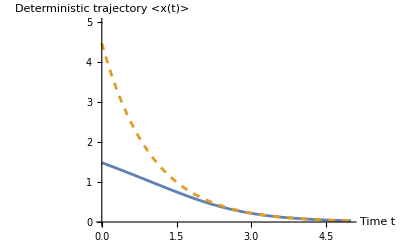

```mathematica
Clear[t,𝒞]
𝒞=3;
Plot[{Sqrt[LambertW[Exp[-2t+𝒞]]],Exp[-t+𝒞/2]},{t,0,5},PlotRange->{0,5},PlotStyle->{Default,Dashed},AxesLabel->{"Time t","Deterministic trajectory <x(t)>"}]
```

## Figure 2 average contribution of noise

1.02882

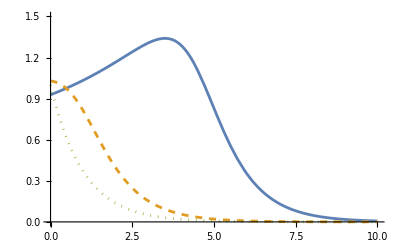

```mathematica
Clear[z0,𝒞,v,t,v0,eq17,Κ]
Κ[v_]:=-v/(1+v^2);
v[t_,𝒞_]:=Sqrt[LambertW[Exp[-2t+𝒞]]];
eq17[t_,𝒞_]:=Κ[v[t,𝒞]]/Κ[Sqrt[Exp[LambertW[𝒞]]]];
eq17[0,0.8]
Plot[{eq17[t,8],eq17[t,0.8],Exp[-t]},{t,0,10},PlotRange->{0,1.5},PlotStyle->{Default,Dashed,Dotted}]
```

## Figure 3 variance of noise contribution

0.374992

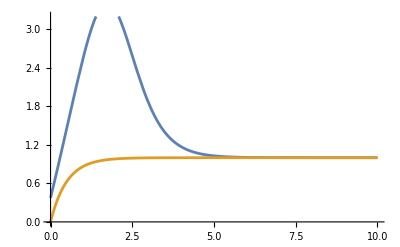

```mathematica
Clear[z0,𝒞,v,t,v0,eq18]
𝒞=3;
z0=Exp[LambertW[𝒞]];
v0=Sqrt[z0];
Κ=-v/(1+v^2);
v=Sqrt[LambertW[Exp[-2t+𝒞]]];
eq18=(2v^(-2)+(v0^4+12t-2v0^(-2))-v^4)/2 Κ^2;
Asymptotic[eq18,t->0]//N
Plot[{eq18,1-Exp[-2t]},{t,0,10},PlotRange->{0,3.2}]
```

## Figure 4 autocorrelation function